# 5,000

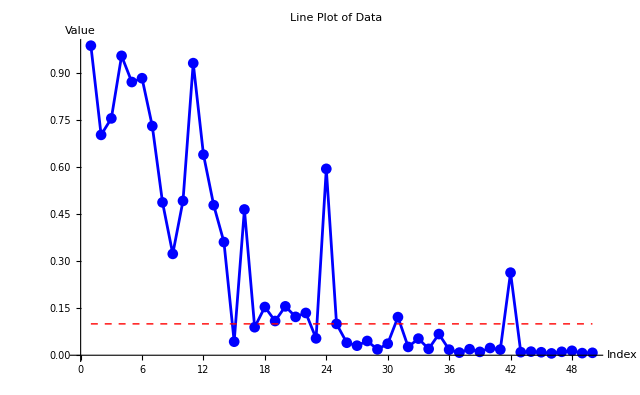

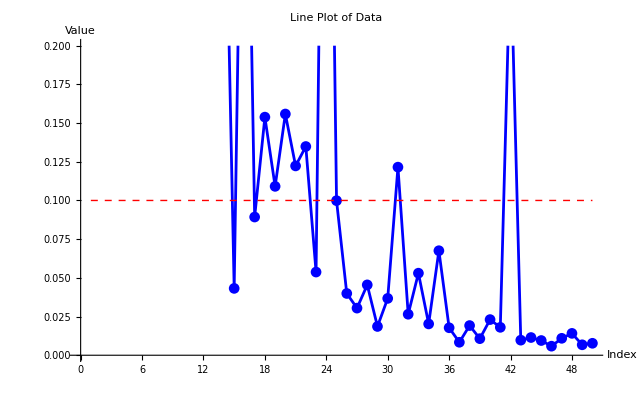

```mathematica
data={{1,0.9871360805513344},{2,0.7026977953056585},{3,0.7553123906136406},{4,0.9547182887086265},{5,0.871252156798082},{6,0.8833714422675267},{7,0.7308313808349319},{8,0.4874239093703157},{9,0.3232382089060842},{10,0.49219900354160157},{11,0.9314522555286701},{12,0.6396110657195284},{13,0.47849106605780267},{14,0.36084745077229863},{15,0.04319120776185436},{16,0.46485201261285775},{17,0.0892976985729669},{18,0.15384323669523614},{19,0.10911016466034099},{20,0.15586248995470878},{21,0.12232204028599224},{22,0.13486131559448716},{23,0.05374689089396629},{24,0.5943888823675875},{25,0.09987632775699605},{26,0.0399076036545015},{27,0.030442170758460143},{28,0.04545937848905572},{29,0.018582068949750303},{30,0.036721408935370126},{31,0.12152341586304993},{32,0.02648659541099203},{33,0.05301685689221282},{34,0.020228840088955383},{35,0.0675317245113119},{36,0.01775254010655215},{37,0.008375133798588693},{38,0.019179537792352565},{39,0.0107032483292585},{40,0.023039054295450972},{41,0.018026322540408233},{42,0.26338032577059095},{43,0.009735838045637128},{44,0.011444017900254956},{45,0.00950935310854541},{46,0.005852255840515742},{47,0.010934011169094158},{48,0.01412408103774194},{49,0.006744180042865684},{50,0.007723694949312705}};

ListLinePlot[data,PlotMarkers->Automatic,PlotStyle->Blue,AxesLabel->{"Index","Value"},PlotLabel->"Line Plot of Data", Epilog->{Red,Dashed,Line[{{1,0.1},{50,0.1}}]}]
ListLinePlot[data,PlotMarkers->Automatic,PlotStyle->Blue,AxesLabel->{"Index","Value"},PlotLabel->"Line Plot of Data", PlotRange->{0, 0.2}, Epilog->{Red,Dashed,Line[{{1,0.1},{50,0.1}}]}]
```

# 16,000

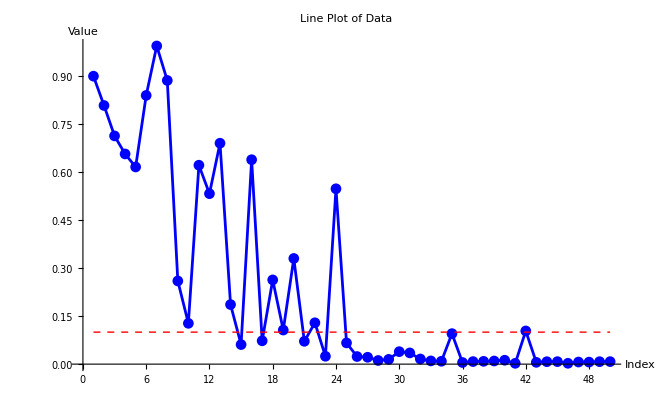

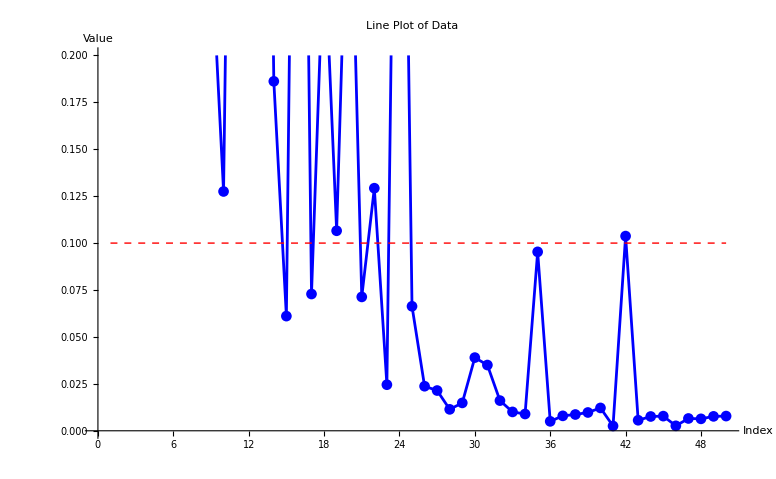

```mathematica
data = {{1,0.900124271236231},{2,0.8085147948493686},{3,0.7133567629341638},{4,0.65697884771398},{5,0.6162812631222258},{6,0.8399812313709385},{7,0.9945527679903151},{8,0.8867831097830455},{9,0.26000847671020216},{10,0.12750652753512487},{11,0.6217922932749491},{12,0.5328286803369089},{13,0.6905230099569977},{14,0.18619360245952415},{15,0.06109537121403773},{16,0.6389861257436846},{17,0.07287271356124912},{18,0.26329429847436797},{19,0.10656956039986648},{20,0.3303419136653863},{21,0.07132372136352622},{22,0.1292524476425594},{23,0.02454696348524072},{24,0.5481428873753031},{25,0.06632692859183546},{26,0.023735554388755242},{27,0.02144129589580072},{28,0.011412253285680714},{29,0.014854094886423242},{30,0.038989026328719006},{31,0.03502823426800646},{32,0.016076961064977077},{33,0.010051037637554909},{34,0.00893790572559},{35,0.0953302193615186},{36,0.005020178756876597},{37,0.007953076382684054},{38,0.00867327934729743},{39,0.009746519319513914},{40,0.012174120043279777},{41,0.002557936419013659},{42,0.10373100122949427},{43,0.005609278328256301},{44,0.007612249340772659},{45,0.007804381238321736},{46,0.0026343997752277183},{47,0.006556684337312},{48,0.006358544485006544},{49,0.007678713280024718},{50,0.007833305669951308}};
ListLinePlot[data,PlotMarkers->Automatic,PlotStyle->Blue,AxesLabel->{"Index","Value"},PlotLabel->"Line Plot of Data", Epilog->{Red,Dashed,Line[{{1,0.1},{50,0.1}}]}]
ListLinePlot[data,PlotMarkers->Automatic,PlotStyle->Blue,AxesLabel->{"Index","Value"},PlotLabel->"Line Plot of Data", PlotRange->{0, 0.2}, Epilog->{Red,Dashed,Line[{{1,0.1},{50,0.1}}]}]
```

# My Q calculations

{{1,25672},{100,157215},{200,318149},{300,499432},{400,667136},{500,847388},{600,1021380},{700,1204700},{800,1356710},{900,1524720},{1000,1681580},{1100,1840670},{1200,1994850},{1300,2.14383×10^6},{1400,2.31771×10^6},{1500,2.49229×10^6},{1600,2.66417×10^6},{1700,2.84364×10^6},{1800,3.0256×10^6},{1900,3.19229×10^6},{2000,3.3512×10^6},{2100,3.5143×10^6},{2200,3.6775×10^6},{2300,3.82743×10^6},{2400,3.9925×10^6},{2500,4.13718×10^6},{2600,4.31397×10^6},{2700,4.48313×10^6},{2800,4.66059×10^6}}

{a→-0.00801827,b→1682.46,c→2962.8}

2962.8+1682.46 x-0.00801827 x^2

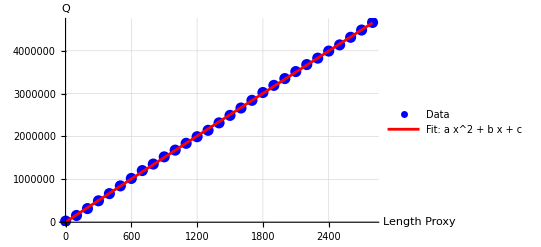

```mathematica
data = {{1,25672},{100,157215},{200,318149},{300,499432},{400,667136},{500,847388},{600,1021380},{700,1204700},{800,1356710},{900,1524720},{1000,1681580},{1100,1840670}, {1200, 1994850},{1300,2143827.497},{1400,2317706.258},{1500,2492287.463},{1600,2664173.602},{1700,2843638.311},{1800,3025599.624},{1900,3192292.203},{2000,3351203.392},{2100,3514297.59},{2200,3677497.932},{2300,3827434.755},{2400,3992496.165},{2500,4137177.412},{2600,4313974.94},{2700, 4483131.006}, {2800,4660589.86755928}, {2900,4837858.959},{3000,5024921.894},{3100,5182497.161},{3200,5351090.259},{3300,5505383.556},{3400,5671128.185}}

fit=FindFit[data,a*x^2+b*x+c,{a,b,c},x]

fittedModel[x_]=a*x^2+b*x+c/. fit

Show[ListPlot[data,PlotStyle->{Blue,PointSize[0.02]},AxesLabel->{"Length Proxy","Q"},PlotLegends->{"Data"}],Plot[fittedModel[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->{Red,Thick},PlotLegends->{"Fit: a x^2 + b x + c"}],PlotRange->All,GridLines->Automatic]
```